```mathematica
Clear[c,m]
c=1;(* sound velocity *)
m=0; (* mass *)
Clear[λ,H0,u,upw,projs]
H0[p_]:=c p PauliMatrix[1]+m c^2 PauliMatrix[3] (* Dirac Hamiltonian *)
u[p_]:=Normalize[#]&/@Eigenvectors[H0[p]] (* normalize eigenvectors *)
λ[p_]:=FullSimplify[Diagonal[u[p].H0[p].Inverse[u[p]]]//ComplexExpand] (*corresponding eigenvalues *)
pw[p_,x_,t_]:=1/(√(2π))Exp[ⅈ (p x  - #[[1]] t)]&/@({λ[p],u[p]}ᵀ) (* plane waves *)
projs[p_]:=FullSimplify[ComplexExpand[Table[PseudoInverse[{v}].{v},{v,u[p]}]]] (* projectors on the eigenvectors *)
```

```mathematica
(* check if eigenvector *)
(#[[1]]*#[[2]]-H0[p].#[[2]])&/@({λ[p],u[p]}ᵀ)//ComplexExpand//FullSimplify//Chop
(#[[1]]*(#[[2]]*#[[3]])-H0[p].(#[[2]]*#[[3]]))&/@({λ[p],u[p],pw[p,x,t]}ᵀ)//ComplexExpand//FullSimplify//Chop
```

{{0,0},{0,0}}

{{0,0},{0,0}}

```mathematica
u[p].H0[p].PseudoInverse[u[p]]//FullSimplify//Chop
```

{{-p,0},{0,p}}

```mathematica
Clear[ψ0,F,σ]
σ=0.5;
ψ0[x_]:=(1/(8 σ^2 π))^(1/4)Exp[-x^2/(4 σ^2)]{1,1}
F[f_,w_]:=FourierTransform[f[t],t,w]
Fψ0[p_]=F[ψ0,p]
(*Clear[Fψ0]
Fψ0[p_]:=Exp[-4 p^2](2/π)^(1/4){1,-1}*)
```

{0.446622 ⅇ^(-0.25 p^2),0.446622 ⅇ^(-0.25 p^2)}

General::munfl: Exp[-1600.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1592.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1584.04] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

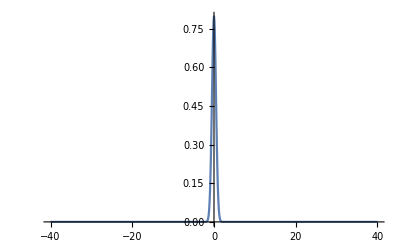

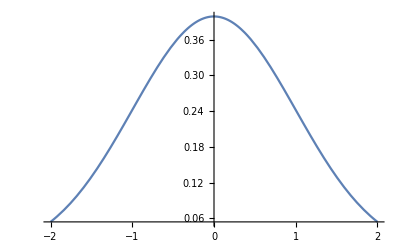

```mathematica
data0=Table[{x,Norm[ψ0[x]]^2},{x,-40,40,0.1}];
ListPlot[data0,PlotRange->Full,Joined->True]
Plot[Norm[Fψ0[p]]^2,{p,-2,2},PlotRange->Full]
```

```mathematica
Fψ0[p]
```

{0.446622 ⅇ^(-0.25 p^2),0.446622 ⅇ^(-0.25 p^2)}

```mathematica
projs[p][[1]]pw[p,x,t][[1]]+projs[p][[2]]pw[p,x,t][[2]]
```

{{ⅇ^(ⅈ (-p t+p x))/(2 √(2 π))+ⅇ^(ⅈ (p t+p x))/(2 √(2 π)),ⅇ^(ⅈ (-p t+p x))/(2 √(2 π))-ⅇ^(ⅈ (p t+p x))/(2 √(2 π))},{ⅇ^(ⅈ (-p t+p x))/(2 √(2 π))-ⅇ^(ⅈ (p t+p x))/(2 √(2 π)),ⅇ^(ⅈ (-p t+p x))/(2 √(2 π))+ⅇ^(ⅈ (p t+p x))/(2 √(2 π))}}

```mathematica
Clear[intarg]
intarg[p_,x_,t_]=FullSimplify[(pw[p,x,t][[1]]*projs[p][[1]]+pw[p,x,t][[2]]*projs[p][[2]]).Fψ0[p]]
```

{0.178176 ⅇ^(p (-0.25 p-ⅈ (t-x))),0.178176 ⅇ^(p (-0.25 p-ⅈ (t-x)))}

```mathematica
nsteps=128;
{min,max}=10σ{-1,1};
xs=Table[x,{x,min,max,(max-min)/(nsteps-1)}];
ts=Table[t,{t,0,max,max/(nsteps-1)}];
data=ParallelTable[{
x,
Norm[
Quiet[
NIntegrate[
intarg[p,x,t],{p,-∞,∞}
,
Method->{Automatic,"SymbolicProcessing"->0}
,
WorkingPrecision->4
]
]
]^2
}
,{t,ts},{x,xs}];
```

```mathematica
cfun[x_]:=Blend[{White,Black},x]
plot=Show[ListDensityPlot[data[[;;,;;,2]],PlotRange->Full,DataRange->{MinMax[xs],MinMax[ts]},PlotRangePadding->0,PlotTheme->"Scientific",ColorFunction->cfun],Plot[c*x{1,-1},{x,Sequence@@MinMax[xs]},PlotStyle->{Dashed,Black}]];
meanPosition=ListPlot[Table[{xs.data[[ti,;;,2]]/Total[data[[ti,;;,2]]],ts[[ti]]},{ti,Length[data]}],Joined->True,PlotTheme->"Scientific"];
Show[plot,meanPosition]
ListPlot[Table[{ts[[ti]],1/σ^2(xs^2).data[[ti,;;,2]]/Total[data[[ti,;;,2]]]},{ti,Length[data]}],Joined->True,PlotTheme->"Scientific"];
```

-Graphics-

```mathematica
H0[p]
```

{{0,p},{p,0}}